```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
rho=Flatten[Import["./kappa.dat"]];
lam1=Flatten[Import["./lam1.dat"]];
lam2=Flatten[Import["./lam2.dat"]];
lam3=Flatten[Import["./lam3.dat"]];
k=Flatten[Import["./k1.dat"]];
rhobar=rho/k;
```

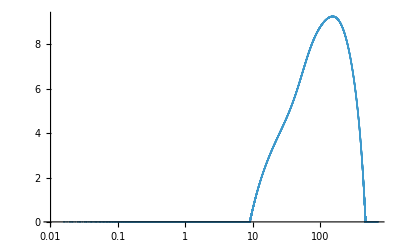

```mathematica
ListPlot[Transpose[{k,rhobar}],PlotRange->All,ScalingFunctions->{"Log",Automatic}]
```

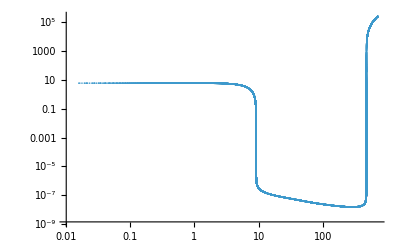

```mathematica
ListPlot[Transpose[{k,lam1}],PlotRange->{All,All},ScalingFunctions->{"Log","Log"}]
```

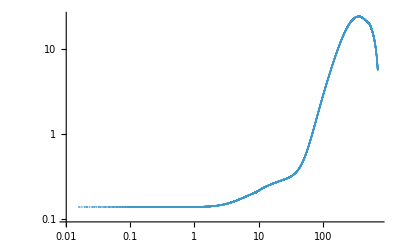

```mathematica
ListPlot[Transpose[{k,lam2}],PlotRange->All,ScalingFunctions->{"Log","Log"}]
```

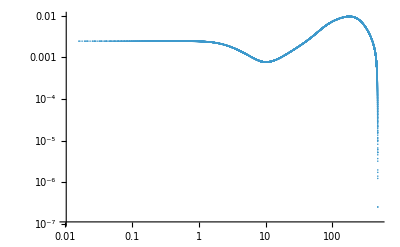

```mathematica
ListPlot[Transpose[{k,lam3}],PlotRange->All,ScalingFunctions->{"Log","Log"}]
```

```mathematica
F[x_]:=lam1[[-1]](x^2/2-rho[[-1]])+lam2[[-1]]/2(x^2/2-rho[[-1]])^2+lam3[[-1]]/6(x^2/2-rho[[-1]])^3
```

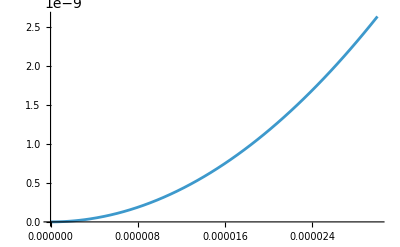

```mathematica
Plot[F[x]-F[0],{x,0,0.00003}]
```